```mathematica
activationfunction[z_]:=1/(1+Exp[-z])
```

## Next

```mathematica
w1=2;
w2=-2;
b= 1;
pE1[x1_,x2_]:=w1*x1+w2*x2+1;
pE1[x1_,x2_]
```

1+2 x1_-2 x2_

```mathematica
2
```

2

## Next

```mathematica
w1=2;
w2=-2;
b=-1;
pE2[x1_,x2_]:=w1*x1+w2*x2+-1;
pE2[x1_,x2_]
```

pE2

## Next

```mathematica
w1=2;
w2=-2;
b=-1;
pE3[x1_,x2_]:=w1*x1+w2*x2 -1;
pE3[x1_,x2_]
```

## Gráficar rectas obtenidas en el ejercicio 1

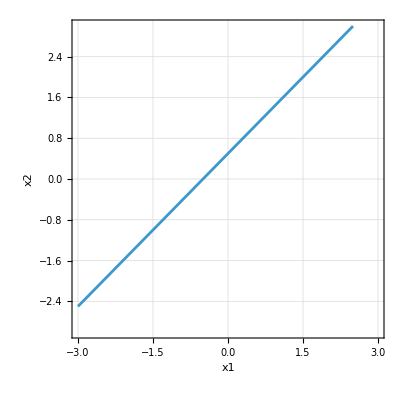

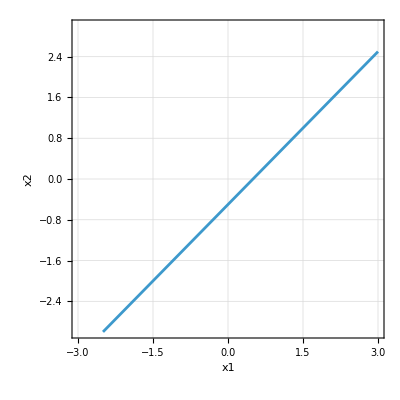

-Graphics-

```mathematica
ContourPlot[pE1[x1,x2]==0,{x1,-3,3},{x2,-3,3},GridLines->Automatic,PlotStyle->{Thick,Red},ContourShading->None,AxesLabel->{"x1","x2"},Axes->True,AxesOrigin->{0,0}]
ContourPlot[pE2[x1,x2]==0,{x1,-3,3},{x2,-3,3},GridLines->Automatic,PlotStyle->{Thick,Red},ContourShading->None,AxesLabel->{"x1","x2"},Axes->True,AxesOrigin->{0,0}]
ContourPlot[pE3[x1,x2]==0,{x1,-3,3},{x2,-3,3},GridLines->Automatic,PlotStyle->{Thick,Red},ContourShading->None,AxesLabel->{"x1","x2"},Axes->True,AxesOrigin->{0,0}]
```

```mathematica
activationfunction[pE1[x1,x2]]
```

1/(1+ⅇ^(-1-2 x1+2 x2))

```mathematica
activationfunction[1+2 x1-2 x2]
```

```mathematica
pf1 =Plot3D[activationfunction[pE1[x1,x2]],{x1,-5,5},{x2,-5,5},PlotStyle->Directive[Opacity[0.7],Blue],AxesLabel->{"x1","x2","a"},PlotLabel->"Activation Function f1(x1, x2)",MeshStyle->Red,ColorFunction->"Rainbow",Boxed->True]
```

-Graphics3D-

```mathematica
pf2=Plot3D[activationfunction[pE2[x1,x2]],{x1,-5,5},{x2,-5,5},PlotStyle->Directive[Opacity[0.7],Blue],AxesLabel->{"x1","x2","a"},PlotLabel->"Activation Function f2(x1, x2)",MeshStyle->Red,ColorFunction->"Rainbow",Boxed->True]
```

-Graphics3D-

```mathematica
pf3 =Plot3D[activationfunction[pE3[x1,x2]],{x1,-5,5},{x2,-5,5},PlotStyle->Directive[Opacity[0.7],Blue],AxesLabel->{"x1","x2","a"},PlotLabel->"Activation Function f(y1h, y2h)",MeshStyle->Red,ColorFunction->"Rainbow",Boxed->True]
```

-Graphics3D-

```mathematica
GraphicsRow[{pf1,pf2,pf3}]
```

-Graphics-

```mathematica
TeXForm[activationfunction[pE1[x1_,x2_]]]
```

\frac{1}{e^{-2 \text{x1$\_$}+2 \text{x2$\_$}-1}+1}

```mathematica
TeXForm[activationfunction[pE2[x1_,x2_]]]
```

\frac{1}{e^{-2 \text{x1$\_$}+2 \text{x2$\_$}+1}+1}

```mathematica
w12 = 2;
w22 =-2;
TeXForm[pE1[x1_,x2_]]
TeXForm[pE2[x1_,x2_]]
f[x1_,x2_]:=w12*activationfunction[pE1[x1,x2]]+w22*activationfunction[pE2[x1,x2]]-1
TeXForm[f[x1_,x2_]]
```

-\frac{2}{e^{-2 \text{x1$\_$}+2 \text{x2$\_$}+1}+1}+\frac{2}{e^{-2 \text{x1$\_$}+2 \text{x2$\_$}-1}+1}-1

```mathematica
Plot3D[f[x1,x2],{x1,-5,5},{x2,-5,5},PlotStyle->Directive[Opacity[0.7],Blue],AxesLabel->{"x1","x2","a"},PlotLabel->"Activation Function activationfunction(wtx[x1, x2])",MeshStyle->Red,ColorFunction->"Rainbow",Boxed->True]
```

```mathematica
points={{0,0},{1,0},{1,1},{0,1}};
yValues=activationfunction/@(pE1@@@points);
yValues
```

{1/(1+1/ⅇ),1/(1+1/ⅇ^3),1/(1+1/ⅇ),1/(1+ⅇ)}

```mathematica
N[{1/(1+1/ⅇ),1/(1+1/ⅇ^3),1/(1+1/ⅇ),1/(1+ⅇ)}]
```

{0.731059,0.952574,0.731059,0.268941}

```mathematica
y2Values=activationfunction/@(pE2@@@points);
y2Values
```

{1/(1+ⅇ),1/(1+1/ⅇ),1/(1+ⅇ),1/(1+ⅇ^3)}

```mathematica
N[{1/(1+ⅇ),1/(1+1/ⅇ),1/(1+ⅇ),1/(1+ⅇ^3)}]
```

{0.268941,0.731059,0.268941,0.0474259}

```mathematica
N[{1/(1+ⅇ),1/(1+1/ⅇ),1/(1+ⅇ),1/(1+ⅇ^3)}]
```

{0.268941,0.731059,0.268941,0.0474259}

{0.731059,0.952574,0.731059,0.268941}

```mathematica
N[y1]
```

0.731059

```mathematica
N[y2]
```

0.952574

```mathematica
N[y3]
```

0.731059

```mathematica
N[y4]
```

0.731059

```mathematica
N[y4]
```

0.731059

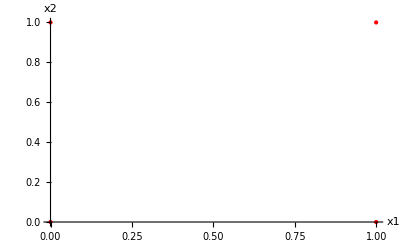

```mathematica
ListPlot[points,AxesLabel->{"x1","x2"},PlotStyle->{Red,PointSize[Large]}]
```

```mathematica
pairs=Transpose[{yValues,y2Values}]
```

{{1/(1+1/ⅇ),1/(1+ⅇ)},{1/(1+1/ⅇ^3),1/(1+1/ⅇ)},{1/(1+1/ⅇ),1/(1+ⅇ)},{1/(1+ⅇ),1/(1+ⅇ^3)}}

```mathematica
yFinalValues=activationfunction/@(pE3@@@pairs);
```

```mathematica
{1/(1+ⅇ^(1-2/(1+1/ⅇ)+2/(1+ⅇ))),1/(1+ⅇ^(1-2/(1+1/ⅇ^3)+2/(1+1/ⅇ))),1/(1+ⅇ^(1-2/(1+1/ⅇ)+2/(1+ⅇ))),1/(1+ⅇ^(1-2/(1+ⅇ)+2/(1+ⅇ^3)))}
```

{1/(1+ⅇ^(1-2/(1+1/ⅇ)+2/(1+ⅇ))),1/(1+ⅇ^(1-2/(1+1/ⅇ^3)+2/(1+1/ⅇ))),1/(1+ⅇ^(1-2/(1+1/ⅇ)+2/(1+ⅇ))),1/(1+ⅇ^(1-2/(1+ⅇ)+2/(1+ⅇ^3)))}

```mathematica
N[{1/(1+ⅇ^(1-2/(1+1/ⅇ)+2/(1+ⅇ))),1/(1+ⅇ^(1-2/(1+1/ⅇ^3)+2/(1+1/ⅇ))),1/(1+ⅇ^(1-2/(1+1/ⅇ)+2/(1+ⅇ))),1/(1+ⅇ^(1-2/(1+ⅇ)+2/(1+ⅇ^3)))}]
```

{0.481068,0.364249,0.481068,0.364249}

```mathematica
{1/(1+1/ⅇ),1/(1+1/ⅇ^3),1/(1+1/ⅇ),1/(1+ⅇ)}
```

{1/(1+1/ⅇ),1/(1+1/ⅇ^3),1/(1+1/ⅇ),1/(1+ⅇ)}

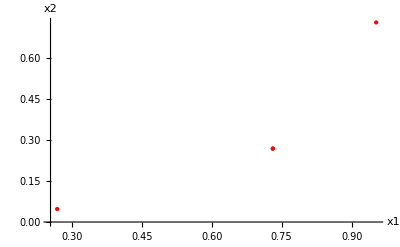

```mathematica
ListPlot[pairs,AxesLabel->{"x1","x2"},PlotStyle->{Red,PointSize[Large]}]
```